```mathematica
f[x_]:=x^2-Cos[x];
```

```mathematica
NewtonRhapsonStep[x_]:=x-f[x]/f'[x];
```

```mathematica
NewtonRhapsonStep[0.5]
```

0.924207

```mathematica
NewtonRhapson[x0_,n_]:=Block[{soluciones={x0},x=x0},
Do[
x=NewtonRhapsonStep[x];
AppendTo[soluciones,x];
,
n
];
soluciones
];
```

```mathematica
listadesoluciones=NewtonRhapson[0.2,10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

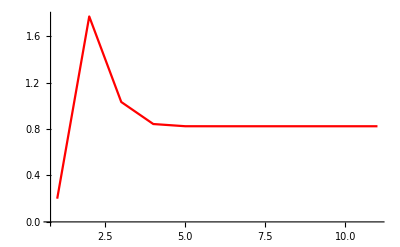

```mathematica
ListLinePlot[listadesoluciones,PlotRange->All,PlotStyle->Red]
```

```mathematica
error[x_]:=-(f''[x])/(2 f'[x]);
```

```mathematica
ListaError=Map[error,listadesoluciones]
```

{-2.48891,-0.19929,-0.429357,-0.547553,-0.562172,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331}

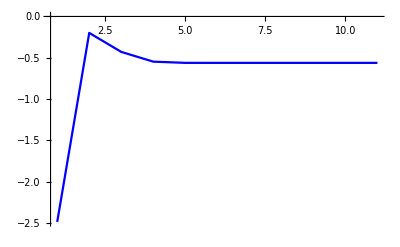

```mathematica
ListLinePlot[ListaError,PlotRange->All,PlotStyle->Blue]
```